## Non-ideal Reversal -- Longfei Fan 09/25/2015

This mathematica notebook file shows all the calculations in the manuscript “Influence of monitoring efficiency on states protection using quantum measurement reversal”.

Main important equations are wrapped in “=====/-------”.

```mathematica
Clear["Global`*"]
```

```mathematica
Assumptions=Abs[α]^2+Abs[β]^2==1;
```

## 1. Single Qubit

```mathematica
Clear["Global`*"]
```

### 1.1 Operators and States

#### Eq. (2)

```mathematica
E0[p_]:=({{1, 0}, {0, √(1-p)}});   (* Eq. (2)*)
E1[p_]:=({{0, √p}, {0, 0}});
X=({{0, 1}, {1, 0}});
ψ0={α,β};
ψ0s={SuperStar[α],SuperStar[β]};
ρ0=({{Abs[α]^2, α SuperStar[β]}, {SuperStar[α] β, Abs[β]^2}});
```

### 1.2 Ideal Reversal

```mathematica
Clear["Global`*"]
```

```mathematica
X.E0[pr].X.E0[d].E0[ps]//MatrixForm
```

(√(1-pr) | 0
0 | √(1-d) √(1-ps))

So it is required that  1 - pr = (1 - d)(1 - ps).

Assume the detection efficiency is 100%. If outcome 0 is observed in the second free damping stage, the system finally evolves to

=============================================================================

```mathematica
ρ1=Simplify[E0[ps].ρ0.Transpose[E0[ps]],0<ps<1];
ρ2r=Simplify[E0[d].ρ1.Transpose[E0[d]],0<d<1];
ρr=Simplify[X.E0[pr].X.ρ2r.X.Transpose[E0[pr]].X,0<pr<1];
```

----------------------------------------------------------------------------------------------------------------------------

#### Eq. (5) and Eq. (6)

```mathematica
ρr//MatrixForm  (* Eq. (5) and Eq. (6)*)
```

(-(-1+pr) Abs[α]^2 | √(-(-1+d) (-1+pr) (-1+ps)) α β^*
√(-(-1+d) (-1+pr) (-1+ps)) β α^* | (-1+d) (-1+ps) Abs[β]^2)

If 1 - pr = (1 - d)(1 - ps) is satisfied, the state is restored.

```mathematica
ρr=ρr/.pr->1-(1-d)(1-ps);
```

```mathematica
ρrs=Simplify[ρr/((1-d)(1-ps)),Assumptions->{0<d<1,0<ps<1}]//MatrixForm
```

(Abs[α]^2 | α β^*
β α^* | Abs[β]^2)

#### Eq. (7): The reversibility R

```mathematica
Clear["Global`*"]
```

```mathematica
Tr[ρr]//Simplify   (* Eq. (7) *)
```

(-1+d) (-1+ps)

Normally, we do not monitor the second stage, so the state finally evolves to

=============================================================================

```mathematica
ρ1=Simplify[E0[ps].ρ0.Transpose[E0[ps]],0<ps<1];
ρ2=Simplify[E0[d].ρ1.Transpose[E0[d]]+E1[d].ρ1.Transpose[E1[d]],0<d<1];
ρ3=Simplify[X.E0[pr].X.ρ2.X.Transpose[E0[pr]].X,0<pr<1];
```

----------------------------------------------------------------------------------------------------------------------------

```mathematica
ρ3=ρ3/.pr->1-(1-d)(1-ps);
```

#### Eq. (8): The successful rate S

```mathematica
Tr[ρr]/Tr[ρ3]//Simplify    (* Eq. (8) *)
```

(Abs[α]^2+Abs[β]^2)/(Abs[α]^2+(1+d-d ps) Abs[β]^2)

### 1.3 Non-ideal Reversal

```mathematica
Clear["Global`*"]
```

#### Eq. (10): State Evolution

According to Eq. (10), we have

=============================================================================

```mathematica
ρ1=Simplify[E0[ps].ρ0.Transpose[E0[ps]]+η E1[ps].ρ0.Transpose[E1[ps]],0<ps<1];
ρ2=Simplify[E0[d].ρ1.Transpose[E0[d]]+E1[d].ρ1.Transpose[E1[d]],0<d<1];
ρ3=Simplify[X.E0[pr].X.ρ2.X.Transpose[E0[pr]].X+ η X.E1[pr].X.ρ2.X.Transpose[E1[pr]].X,0<pr<1];
```

----------------------------------------------------------------------------------------------------------------------------

```mathematica
ρ3=ρ3/.pr->1-(1-d)(1-ps);
```

```mathematica
ρ1//MatrixForm
```

(Abs[α]^2+ps η Abs[β]^2 | √(1-ps) α β^*
√(1-ps) β α^* | -(-1+ps) Abs[β]^2)

```mathematica
ρ2//MatrixForm
```

(Abs[α]^2+(d-d ps+ps η) Abs[β]^2 | √((-1+d) (-1+ps)) α β^*
√((-1+d) (-1+ps)) β α^* | (-1+d) (-1+ps) Abs[β]^2)

```mathematica
ρ3//MatrixForm
```

((1-d) (1-ps) (Abs[α]^2+(d-d ps+ps η) Abs[β]^2) | √((1-d) (-1+d) (1-ps) (-1+ps)) α β^*
√((1-d) (-1+d) (1-ps) (-1+ps)) β α^* | (-1+d) (-1+ps) Abs[β]^2+(1-(1-d) (1-ps)) η (Abs[α]^2+(d-d ps+ps η) Abs[β]^2))

```mathematica
ρ3=ρ3/.pr->1-(1-d)(1-ps);
```

#### Eq. (11) and Eq. (12): Final State

Simplify and normalize above matrix, we get

=============================================================================

```mathematica
MM[d_,ps_,η_]:=d(1-ps)+η ps;    (* Eq. (11) and Eq. (12)*)
NN[d_,ps_]:=1/((1-d)(1-ps))-1;
A3[d_,ps_,η_,a_,b_]:=1+MM[d,ps,η] b^2+η NN[d,ps](a^2+MM[d,ps,η] b^2);
```

```mathematica
ρ[d_,ps_,η_,a_,b_]:=1/A3[d,ps,η,a,b]{{a^2+MM[d,ps,η] b^2,a b},{a b,b^2+η NN[d,ps](a^2+MM[d,ps,η] b^2)}};
```

----------------------------------------------------------------------------------------------------------------------------

```mathematica
Simplify[Tr[ρ[d,ps,η,a,b]],Assumptions->a^2+b^2==1]
```

1

#### Eq. (13): Reversibility

The reversibility is given by

```mathematica
Simplify[Tr[X.E0[pr].X.E0[d].E0[ps].ρ0.Transpose[X.E0[pr].X.E0[d].E0[ps]]]/.pr->1-(1-d)(1-ps)]
```

(-1+d) (-1+ps) (Abs[α]^2+Abs[β]^2)

#### Eq. (14): Success Rate

The success rate is given be

```mathematica
SS[d_,ps_,η_,a_,b_]:=1/A3[d,ps,η,a,b];
```

#### Eq. (15): Fidelity

```mathematica
FullSimplify[{{a,b}}.{{a^2+M b^2,a b},{a b,b^2+η N(a^2+M b^2)}}.Transpose[{{a,b}}]][[1,1]]
```

a^4+a^2 b^2 (2+M+N η)+b^4 (1+M N η)

```mathematica
FF[d_,ps_,η_,a_,b_]:=1/A3[d,ps,η,a,b](1+(MM[d,ps,η]+η NN[d,ps])a^2 b^2+η MM[d,ps,η]NN[d,ps] b^4);
```

#### Fig. 2(a): Fidelity with respect to p_s under different η

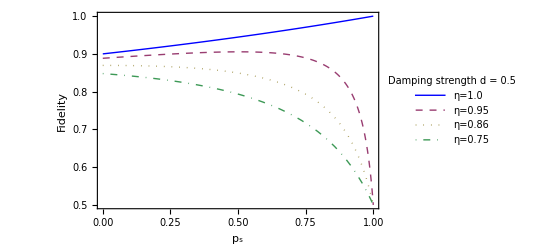

```mathematica
Plot[
{
FF[0.5,ps,0.0,1/(√2),1/(√2)],
FF[0.5,ps,0.05,1/(√2),1/(√2)],
FF[0.5,ps,0.13745,1/(√2),1/(√2)],
FF[0.5,ps,0.25,1/(√2),1/(√2)]
},
{ps,0,1},
PlotRange->Full,
Frame->True,
FrameLabel->{"p_s","Fidelity"},
RotateLabel->True,
FrameStyle->Directive[Black],
FrameTicks->{{All,All},{All,All}},
PlotLegends->Placed[LineLegend[
{"η=1.0","η=0.95","η=0.86","η=0.75"},
LegendLabel->"Damping strength d = 0.5",
LegendLayout->{"Row",2}],
{Left,Bottom}
],
PlotStyle->{Blue,Dashed,Dotted,DotDashed},
BaseStyle->{FontFamily->"Times",FontSize->12}]
```

#### Fig. 2(b): Success Rate with respect to p_s under different η

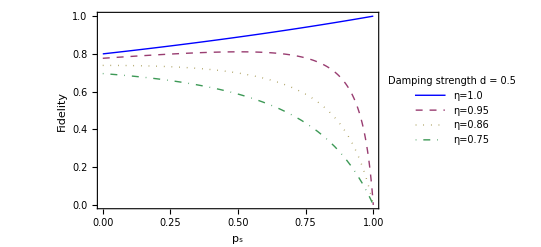

```mathematica
Plot[
{
SS[0.5,ps,0.0,1/(√2),1/(√2)],
SS[0.5,ps,0.05,1/(√2),1/(√2)],
SS[0.5,ps,0.13745,1/(√2),1/(√2)],
SS[0.5,ps,0.25,1/(√2),1/(√2)]
},
{ps,0,1},
PlotRange->Full,
Frame->True,
FrameLabel->{"p_s","Fidelity"},
RotateLabel->True,
FrameStyle->Directive[Black],
FrameTicks->{{All,All},{All,All}},
PlotLegends->Placed[LineLegend[
{"η=1.0","η=0.95","η=0.86","η=0.75"},
LegendLabel->"Damping strength d = 0.5",
LegendLayout->{"Row",2}],
{Left,Bottom}
],
PlotStyle->{Blue,Dashed,Dotted,DotDashed},
BaseStyle->{FontFamily->"Times",FontSize->12}]
```

#### Eq. (16): The Critical Value of η

```mathematica
solution=D[A3[d,ps,η,a,b],ps]/.{ps->0,a^2->1-b^2}
```

((1-b^2+b^2 d) η)/(1-d)+b^2 (-d+η)+b^2 (-1+1/(1-d)) η (-d+η)

```mathematica
solution/.η->0
```

-b^2 d

=============================================================================

```mathematica
Solve[solution==0,η]//Simplify
```

{{η→-(1-b^2 d^2+√(1-2 b^2 d^2+b^4 (-2+d)^2 d^2))/(2 b^2 d)},{η→(-1+b^2 d^2+√(1-2 b^2 d^2+b^4 (-2+d)^2 d^2))/(2 b^2 d)}}

----------------------------------------------------------------------------------------------------------------------------

So the critical value of 1-η

```mathematica
etabar[d_,b_]:=1/2(d-1/(d b^2)+√((d-1/(d b^2))^2+4(1-d)));
```

```mathematica
diff=D[A3[d,ps,η,a,b],ps]/.{a^2->1-b^2}
```

b^2 (-d+η)+b^2 (-1+1/((1-d) (1-ps))) η (-d+η)+(η (1-b^2+b^2 (d (1-ps)+ps η)))/((1-d) (1-ps)^2)

```mathematica
Solve[diff==0,ps]//FullSimplify
```

{{ps→1+((-1-b^2 (-1+η)) η)/(√(b^2 (-1+d) (1+b^2 (-1+η)) (d-η) (-1+η) η))},{ps→1+((1+b^2 (-1+η)) η)/(√(b^2 (-1+d) (1+b^2 (-1+η)) (d-η) (-1+η) η))}}

```mathematica
psopt[d_,η_,b_]:=1-√((η(1-b^2 (1-η)))/(b^2 (1-d)  (d-η) (1-η)));
```

```mathematica
Solve[1-√((η(1-b^2 (1-η)))/(b^2 (1-d)  (d-η) (1-η)))==0,η]
```

{{η→(-1/b^2+d^2-√(4 (1-d) d^2+(1/b^2-d^2)^2))/(2 d)},{η→(-1/b^2+d^2+√(4 (1-d) d^2+(1/b^2-d^2)^2))/(2 d)}}

```mathematica
FindRoot[D[SS[0.5,ps,0.05,1/(√2),1/(√2)],ps],{ps,0.5}]
```

{ps→0.504405}

```mathematica
psopt[0.5,0.05,1/(√2)]
```

0.504405

```mathematica
psopt[0.5,0,1/(√2)]
```

psopt[0,5,0,1/(√2)]

```mathematica
Plot[
psopt[0.5,η,1/(√2)],
{η,0,0.13745}，
PlotRange->Full,
Frame->True]
```

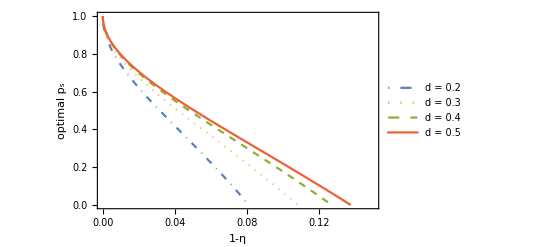

```mathematica
Plot[
{psopt[0.2,η,1/(√2)],
psopt[0.3,η,1/(√2)],
psopt[0.4,η,1/(√2)],
psopt[0.5,η,1/(√2)]},
{η,0,0.15} ,
PlotRange->{0,1},
Frame->True,
FrameLabel->{"1-η","optimal p_s"},
FrameStyle->Directive[Black],
FrameTicks->{{All,All},{All,All}},
PlotLegends->Placed[LineLegend[
{"d = 0.2","d = 0.3","d = 0.4","d = 0.5"},
LegendLayout->{"Row",4}],
{Right,Top}
],
PlotStyle->{DotDashed,Dotted,Dashed,Line[{{0,0},{2,1}}]},
BaseStyle->{FontFamily->"Times",FontSize->12}]
```

#### Fig. 3

```mathematica
Plot3D[etabar[d,b],
{d,0,1},{b,0,1},
PlotRange->Full,
AxesLabel->{"d","|β|","(η^-)_c"},
ColorFunction->Function[{x,y,z},Hue[.65(1-z)]],
BaseStyle->{FontFamily->"Times", FontSize->12}
]
```

```mathematica
?Plot3D
```

```mathematica
DensityPlot[etabar[d,b],
{d,0,1},{b,0,1},
PlotRange->Full,
FrameLabel->{"d","|β|"},
ColorFunction->"Rainbow",
PlotLegends->BarLegend[
Automatic,
LegendMarkerSize->280,
LegendLabel->"(η^-)_c"],
BaseStyle->{FontFamily->"Times", FontSize->12}
]
```

-Graphics-

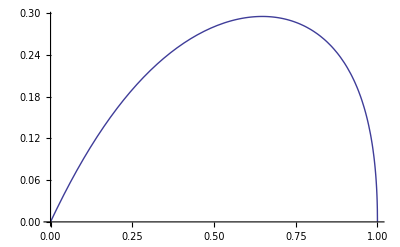

```mathematica
Plot[etabar[d,1],{d,0,1}]
```

```mathematica
FindMaximum[etabar[d,1],{d,0.5}]
```

{0.295598,{d→0.647799}}

## 2. Entangled Qubits

```mathematica
Clear["Global`*"]
```

### 2.1 Operators and States

```mathematica
pr=1-(1-d)(1-p);
```

```mathematica
Clear["pr"];
```

```mathematica
E0[p_]:=({{1, 0}, {0, √(1-p)}});
E1[p_]:=({{0, √p}, {0, 0}});
X=({{0, 1}, {1, 0}});
Y=({{0, -I}, {I, 0}});
E00[x_,y_]:=KroneckerProduct[E0[x],E0[y]];
E01[x_,y_]:=KroneckerProduct[E0[x],E1[y]];
E10[x_,y_]:=KroneckerProduct[E1[x],E0[y]];
E11[x_,y_]:=KroneckerProduct[E1[x],E1[y]];
XX=KroneckerProduct[X,X];
YY=KroneckerProduct[Y,Y];
```

### 2.2 State Evolution Operators

#### In each step, we have 4 possible outcomes E_ij,i,j=0,1. Therefore, after the three-stage scheme, we have 4^3=64 possible outcomes, for each we get an evolution operator and a corresponding density matrix. We have to add all the 64 density matrices together to get the total density operator.

#### Firstly, let us calculate the 64 evolution operator M.

#### We calculate M seperately in four steps. For each one, the operator in the second stage is given, meanwhile operators in other tow stages iterate over 4 possible choice.

#### 1> M00: E00 is chosen the second stage.

```mathematica
MM00=Simplify[
Table[
XX.Mk.XX.E00[d,d].Mj.ρ0.Transpose[XX.Mk.XX.E00[d,d].Mj],(* E00 is chosen *)
{Mk,{E00[pr,pr],E01[pr,pr],E10[pr,pr],E11[pr,pr]}}, (* Mk iterates *)
{Mj,{E00[p,p],E01[p,p],E10[p,p],E11[p,p]}}
],
{0<p<1,0<d<1}
];
MM00//MatrixForm;
```

#### 2> M01: E01 is chosen in the second stage

```mathematica
MM01=Simplify[
Table[
XX.Mk.XX.E01[d,d].Mj.ρ0.Transpose[XX.Mk.XX.E01[d,d].Mj],
{Mk,{E00[pr,pr],E01[pr,pr],E10[pr,pr],E11[pr,pr]}},
{Mj,{E00[p,p],E01[p,p],E10[p,p],E11[p,p]}}
],
{0<p<1,0<d<1}
];
MM01//MatrixForm;
```

#### 3> M10: E10 is chosen in the second stage

```mathematica
MM10=Simplify[
Table[
XX.Mk.XX.E10[d,d].Mj.ρ0.Transpose[XX.Mk.XX.E10[d,d].Mj],
{Mk,{E00[pr,pr],E01[pr,pr],E10[pr,pr],E11[pr,pr]}},
{Mj,{E00[p,p],E01[p,p],E10[p,p],E11[p,p]}}
],
{0<p<1,0<d<1}
];
MM10//MatrixForm;
```

#### 4> M11: E11 is chosen in the second stage

```mathematica
MM11=Simplify[
Table[
XX.Mk.XX.E11[d,d].Mj.ρ0.Transpose[XX.Mk.XX.E11[d,d].Mj],
{Mk,{E00[pr,pr],E01[pr,pr],E10[pr,pr],E11[pr,pr]}},
{Mj,{E00[p,p],E01[p,p],E10[p,p],E11[p,p]}}
],
{0<p<1,0<d<1}
];
MM11//MatrixForm;
```

#### Finally, we get 64 evolution operators.

```mathematica
MMs=List[MM00,MM01,MM10,MM11];
```

#### However, since we monitor the environment, the probabilities to get each outcome should be modified by η.

```mathematica
PP=Table[
p1*p2,
{p1,{1,η,η,η^2}},
{p2,{1,η,η,η^2}}
];
PP//MatrixForm;
```

### 2.3 Fianl Mixed States

#### 1> α,δ=0: Eq. (21)

```mathematica
ψ1={0,β,γ,0};
ψ0={0,SuperStar[β],SuperStar[γ],0};
ρ0=KroneckerProduct[ψ1,ψ0];
ρ0//MatrixForm;
```

#### The evolution is given by

=============================================================================

```mathematica
ρr=Module[
{i,j,k,ρ},
ρ=DiagonalMatrix[{0,0,0,0}];
For[i=1,i≤4,i++,
For[j=1,j≤4,j++,
For[k=1,k≤4,k++,
ρ=ρ+PP[[j,k]]*MMs[[i]][[j,k]]
]
]
];
ρ//FullSimplify
];
```

----------------------------------------------------------------------------------------------------------------------------

#### The state evolves to Eq. (22)

```mathematica
ρr//MatrixForm
```

(-(-1+pr)^2 (d (-1+p)-p η) (β β^*+γ γ^*) | 0 | 0 | 0
0 | (-1+pr) (β (-1+p-p pr η^2+d (-1+p) (-1+pr η)) β^*-pr γ η (d-d p+p η) γ^*) | -(-1+d) (-1+p) (-1+pr) β γ^* | 0
0 | -(-1+d) (-1+p) (-1+pr) γ β^* | (-1+pr) (-pr β η (d-d p+p η) β^*+γ (-1+p-p pr η^2+d (-1+p) (-1+pr η)) γ^*) | 0
0 | 0 | 0 | -pr η (-1+p-p pr η^2+d (-1+p) (-1+pr η)) (β β^*+γ γ^*))

#### The normalized fator

```mathematica
Ar=Tr[ρr]//FullSimplify
```

(1+pr (-1+η)) (1+d pr (-1+η)+p (-1+η) (1-d pr+pr η)) (β β^*+γ γ^*)

#### Elements in lists

```mathematica
For[
i=1,i≤4,i++,
For[
j=1,j≤4,j++,
Print[ρr[[i,j]]]
]
];
```

-(-1+pr)^2 (d (-1+p)-p η) (β β^*+γ γ^*)

0

0

0

«1 more identical outputs»

(-1+pr) (β (-1+p-p pr η^2+d (-1+p) (-1+pr η)) β^*-pr γ η (d-d p+p η) γ^*)

-(-1+d) (-1+p) (-1+pr) β γ^*

0

0

-(-1+d) (-1+p) (-1+pr) γ β^*

(-1+pr) (-pr β η (d-d p+p η) β^*+γ (-1+p-p pr η^2+d (-1+p) (-1+pr η)) γ^*)

0

0

0

«1 more identical outputs»

-pr η (-1+p-p pr η^2+d (-1+p) (-1+pr η)) (β β^*+γ γ^*)

#### 2> β,γ=0, Eq. (24)

```mathematica
ϕ0={SuperStar[α],0,0,SuperStar[δ]};
ϕ1={α,0,0,δ};
ρ0=KroneckerProduct[ϕ1,ϕ0];
ρ0//MatrixForm;
```

#### The evolution is given by

=============================================================================

```mathematica
ρr=Module[
{i,j,k,ρ},
ρ=DiagonalMatrix[{0,0,0,0}];
For[i=1,i≤4,i++,
For[j=1,j≤4,j++,
For[k=1,k≤4,k++,
ρ=ρ+PP[[j,k]]*MMs[[i]][[j,k]]
]
]
];
ρ//FullSimplify
];
```

----------------------------------------------------------------------------------------------------------------------------

#### The state evolves to Eq. (22)

```mathematica
ρr//MatrixForm
```

((-1+pr)^2 (α α^*+δ (d-d p+p η)^2 δ^*) | 0 | 0 | -(-1+d) (-1+p) (-1+pr) α δ^*
0 | (-1+pr) (-pr α η α^*-δ (d (-1+p)-p η) (-1+p-p pr η^2+d (-1+p) (-1+pr η)) δ^*) | 0 | 0
0 | 0 | (-1+pr) (-pr α η α^*-δ (d (-1+p)-p η) (-1+p-p pr η^2+d (-1+p) (-1+pr η)) δ^*) | 0
-(-1+d) (-1+p) (-1+pr) δ α^* | 0 | 0 | pr^2 α η^2 α^*+δ (-1+p-p pr η^2+d (-1+p) (-1+pr η))^2 δ^*)

#### The normalized fator

```mathematica
Ar=Tr[ρr]//FullSimplify
```

α (1+pr (-1+η))^2 α^*+δ (-1+d pr-d pr η+p (-1+η) (-1+d pr-pr η))^2 δ^*

#### Elements in lists

```mathematica
For[
i=1,i≤4,i++,
For[
j=1,j≤4,j++,
Print[ρr[[i,j]]]
]
];
```

(-1+pr)^2 (α α^*+δ (d-d p+p η)^2 δ^*)

0

0

-(-1+d) (-1+p) (-1+pr) α δ^*

0

(-1+pr) (-pr α η α^*-δ (d (-1+p)-p η) (-1+p-p pr η^2+d (-1+p) (-1+pr η)) δ^*)

0

0

0

«1 more identical outputs»

(-1+pr) (-pr α η α^*-δ (d (-1+p)-p η) (-1+p-p pr η^2+d (-1+p) (-1+pr η)) δ^*)

0

-(-1+d) (-1+p) (-1+pr) δ α^*

0

0

pr^2 α η^2 α^*+δ (-1+p-p pr η^2+d (-1+p) (-1+pr η))^2 δ^*

### 2.4 Concurrence